# ChaoticHash2

## Time Series Dependent on Input String ChaoticHash2

```mathematica
ComputeTotalTime[input_]:=Module[{asciiSum},asciiSum=Total[ToCharacterCode[input]];
5+Rescale[asciiSum,{0,255*StringLength[input]},{0,10}]]
```

```mathematica
SelectSimulationParameters[input_]:=Module[{asciiValues,length,increment,positions,selectedValues,normalizedValues,m1,m2,l1,l2,mMin,mMax,lMin,lMax},asciiValues=ToCharacterCode[input];
length=Length[asciiValues];
increment=First[Select[Range[2,Max[2,length-1]],CoprimeQ[#,length]&]];
positions=Mod[Range[0,length-1]*increment,length]+1;
selectedValues=asciiValues[[positions]];
normalizedValues=Rescale[selectedValues,{0,255},{0,1}];
mMin=0.5;mMax=5.0;
lMin=0.5;lMax=5.0;
m1=mMin+Mean[Take[normalizedValues,{1,-1,4}]]*(mMax-mMin);
m2=mMin+Mean[Take[normalizedValues,{2,-1,4}]]*(mMax-mMin);
l1=lMin+Mean[Take[normalizedValues,{3,-1,4}]]*(lMax-lMin);
l2=lMin+Mean[Take[normalizedValues,{4,-1,4}]]*(lMax-lMin);
{m1,m2,l1,l2}]
```

```mathematica
CreateInitialConditions[m1_,m2_,l1_,l2_]:=Module[{theta1,theta2,omega1,omega2,x1Init,y1Init,x1DotInit,y1DotInit,x2Init,y2Init,x2DotInit,y2DotInit},theta1=Pi/2;theta2=Pi/2;
omega1=0;omega2=0;
x1Init=l1*Sin[theta1];
y1Init=-l1*Cos[theta1];
x2Init=x1Init+l2*Sin[theta2];
y2Init=y1Init-l2*Cos[theta2];
x1DotInit=0;
y1DotInit=0;
x2DotInit=0;
y2DotInit=0;
{x1[0]==x1Init,y1[0]==y1Init,x2[0]==x2Init,y2[0]==y2Init,x1'[0]==x1DotInit,y1'[0]==y1DotInit,x2'[0]==x2DotInit,y2'[0]==y2DotInit}]
```

```mathematica
SolveConstraintDPSimulation[{m1_,m2_,l1_,l2_},initialConditions_,totalTime_]:=Module[{g,params,deqns,aeqns,allInitialConditions,soldp},g=10;params={Subscript[m,1]->m1,Subscript[m,2]->m2,Subscript[l,1]->l1,Subscript[l,2]->l2,g->g};
deqns={Subscript[m,1] x1''[t]==(λ1[t]/Subscript[l,1]) x1[t]-(λ2[t]/Subscript[l,2]) (x2[t]-x1[t]),Subscript[m,1] y1''[t]==(λ1[t]/Subscript[l,1]) y1[t]-(λ2[t]/Subscript[l,2]) (y2[t]-y1[t])-Subscript[m,1] g,Subscript[m,2] x2''[t]==(λ2[t]/Subscript[l,2]) (x2[t]-x1[t]),Subscript[m,2] y2''[t]==(λ2[t]/Subscript[l,2]) (y2[t]-y1[t])-Subscript[m,2] g};
aeqns={x1[t]^2+y1[t]^2==Subscript[l,1]^2,(x2[t]-x1[t])^2+(y2[t]-y1[t])^2==Subscript[l,2]^2};
allInitialConditions=Join[initialConditions,{x1'[0]==0,y1'[0]==0,x2'[0]==0,y2'[0]==0} (*Include derivatives*)];
soldp=First[NDSolve[{deqns,aeqns,allInitialConditions}/. params,{x1,y1,x2,y2,λ1,λ2},{t,0,totalTime},Method->{"IndexReduction"->{"Pantelides","ConstraintMethod"->"Projection"}}]];
soldp]
```

```mathematica
SolveConstraintDPSimulation[{m1_,m2_,l1_,l2_},initialConditions_,totalTime_]:=Module[{g,params,deqns,aeqns,allInitialConditions,soldp},g=10;params={Subscript[m,1]->m1,Subscript[m,2]->m2,Subscript[l,1]->l1,Subscript[l,2]->l2,g->g};
deqns={Subscript[m,1] x1''[t]==(λ1[t]/Subscript[l,1]) x1[t]-(λ2[t]/Subscript[l,2]) (x2[t]-x1[t]),Subscript[m,1] y1''[t]==(λ1[t]/Subscript[l,1]) y1[t]-(λ2[t]/Subscript[l,2]) (y2[t]-y1[t])-Subscript[m,1] g,Subscript[m,2] x2''[t]==(λ2[t]/Subscript[l,2]) (x2[t]-x1[t]),Subscript[m,2] y2''[t]==(λ2[t]/Subscript[l,2]) (y2[t]-y1[t])-Subscript[m,2] g};
aeqns={x1[t]^2+y1[t]^2==Subscript[l,1]^2,(x2[t]-x1[t])^2+(y2[t]-y1[t])^2==Subscript[l,2]^2};
allInitialConditions=initialConditions;
soldp=First[NDSolve[{deqns,aeqns,allInitialConditions}/. params,{x1,y1,x2,y2,λ1,λ2},{t,0,totalTime},Method->{"IndexReduction"->{"Pantelides","ConstraintMethod"->"Projection"}}]];
soldp]
```

```mathematica
ChaoticHash2[inputString_String]:=Module[{m1,m2,l1,l2,initialConditions,totalTime,soldp,combinedData,normalizedData,integerData,byteData,byteArray,hashOutput},totalTime=ComputeTotalTime[inputString];
{m1,m2,l1,l2}=SelectSimulationParameters[inputString];
initialConditions=CreateInitialConditions[m1,m2,l1,l2];
soldp=SolveConstraintDPSimulation[{m1,m2,l1,l2},initialConditions,totalTime];
combinedData=ExtractSimulationData[soldp,totalTime];
normalizedData=Rescale[combinedData,MinMax[combinedData],{0,255}];
integerData=Round[normalizedData];
byteData=IntegerDigits[integerData,256,1];
byteArray=FromDigits[Flatten[byteData],256];
hashOutput=IntegerString[Hash[byteArray,"SHA256"],16,64];
hashOutput]
```

```mathematica
ChaoticHash2["Hello world"]
```

a0190fb560e08308c12cad04fb41314baf0c1c583b18b5720855a12b04c478d7

```mathematica
ChaoticHash2["hello world"]
```

0a8c302fe888d5f3e358120010c7ef22d222cfc17659b2996b4237b946fcd759

## Hamming Distance ChaoticHash2

```mathematica
testStrings={"TestString","testString"};
customHashes=ChaoticHash2/@testStrings;
hashFunctions={"MD5","SHA1","SHA224","SHA256","Adler32","CRC32"};
```

```mathematica
hammingDistances=Map[Function[func,hashes=IntegerString[Hash[#,func],16]&/@testStrings;
dist=HammingDistanceHex[hashes[[1]],hashes[[2]]];
{func,dist}],hashFunctions];

customDist=HammingDistanceHex[customHashes[[1]],customHashes[[2]]];
hammingDistances=Append[hammingDistances,{"ChaoticHash2",customDist}];

Grid[Prepend[hammingDistances,{"Hash Function","Hamming Distance"}],Frame->All]
```

Hash Function | Hamming Distance
MD5 | 65
SHA1 | 79
SHA224 | 112
SHA256 | 113
Adler32 | 3
CRC32 | 15
ChaoticHash2 | 143

## Bit Distribution ChaoticHash2 for 50 Random Strings

```mathematica
randomStrings=Table[StringJoin[RandomChoice[CharacterRange["A","Z"]~Join~CharacterRange["a","z"]~Join~CharacterRange["0","9"],RandomInteger[{8,16}]]],{50}];

computeBitCounts[hashFunc_,inputStrings_]:=Total[IntegerDigits[#,2]]&/@(Hash[#,hashFunc]&/@inputStrings);

computeChaoticBitCounts[inputStrings_]:=ParallelMap[Total[IntegerDigits[#,2]]&[Hash[ChaoticHash2[#],"SHA256"]]&,inputStrings];

bitDistributions=Association[#->computeBitCounts[#,randomStrings]&/@hashFunctions];

bitDistributions["ChaoticHash2"]=computeChaoticBitCounts[randomStrings];

bitDistributions
```

<|SHA256→{135,134,136,130,128,124,123,115,111,126,132,127,125,123,142,131,126,126,107,129,131,135,119,119,127,127,132,123,133,128,127,131,132,127,132,119,143,144,125,130,140,133,133,118,135,130,143,127,132,144},SHA224→{111,108,107,109,113,115,117,111,106,112,108,116,118,121,111,110,102,103,116,123,107,103,110,104,112,115,117,113,115,126,116,107,100,117,121,109,112,117,110,114,112,111,107,98,116,115,111,103,99,104},MD5→{68,67,70,66,63,62,73,56,65,69,50,60,70,69,65,63,54,64,73,58,62,64,58,65,64,64,65,59,63,58,71,61,69,69,73,64,71,61,68,61,69,60,70,70,64,67,59,63,64,63},ChaoticHash2→{130,126,130,128,135,121,146,127,138,135,116,139,140,123,119,125,133,123,134,136,132,140,134,118,114,130,140,130,118,131,131,127,142,132,120,134,119,115,125,118,129,134,135,129,143,129,125,130,135,122}|>

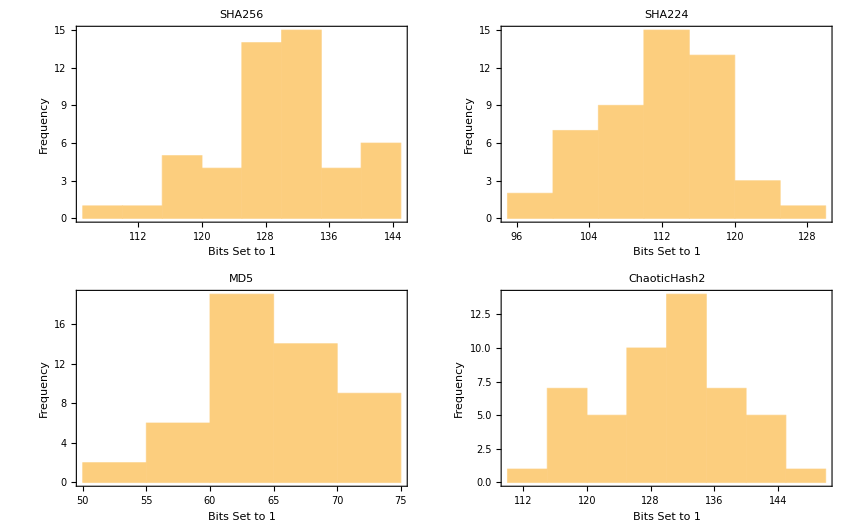

```mathematica
histograms=Table[Histogram[bitDistributions[hashFunc],PlotLabel->hashFunc,Frame->True,AxesLabel->{"Bits Set to 1","Frequency"}],{hashFunc,Keys[bitDistributions]}];

GraphicsGrid[Partition[histograms,UpTo[2]],Spacings->{0.5,1}]
```

## Pearson Chi-Square Test for 50 Strings

```mathematica
uniformityTests=Table[{hashFunc,PearsonChiSquareTest[bitDistributions[hashFunc]]},{hashFunc,Keys[bitDistributions]}];

Grid[Prepend[uniformityTests,{"Hash Function","p-Value"}],Frame->All]
```

Hash Function | p-Value
SHA256 | 0.0511814
SHA224 | 0.449997
MD5 | 0.267336
ChaoticHash2 | 0.332594

## Entropy Test for 50 Strings

```mathematica
entropyValues=Table[{hashFunc,N@Entropy[bitDistributions[hashFunc]]},{hashFunc,Keys[bitDistributions]}];

Grid[Prepend[entropyValues,{"Hash Function","Entropy"}],Frame->All]
```

Hash Function | Entropy
SHA256 | 2.96375
SHA224 | 2.9261
MD5 | 2.7318
ChaoticHash2 | 3.12698

## Bit Distribution ChaoticHash2 for 500 Random Strings

```mathematica
randomStrings500=ParallelTable[StringJoin[RandomChoice[CharacterRange["A","Z"]~Join~CharacterRange["a","z"]~Join~CharacterRange["0","9"],RandomInteger[{8,16}]]],{500}];

computeParallelBitCounts500[hashFunc_,inputStrings_]:=ParallelMap[Total[IntegerDigits[#,2]]&[Hash[#,hashFunc]]&,inputStrings];

computeChaoticBitCounts500[inputStrings_]:=ParallelMap[Total[IntegerDigits[#,2]]&[Hash[ChaoticHash2[#],"SHA256"]]&,inputStrings];

bitDistributions500=Association[#->computeParallelBitCounts500[#,randomStrings500]&/@{"SHA256","SHA224","MD5"}];

bitDistributions500["ChaoticHash2"]=computeChaoticBitCounts500[randomStrings500]
```

{130,126,135,112,143,130,125,136,123,133,120,133,132,130,135,122,120,133,108,138,117,128,131,131,124,128,139,118,134,127,118,127,126,122,122,136,119,135,129,126,145,127,121,141,131,129,138,116,127,134,117,124,139,137,116,135,114,117,122,124,135,134,125,114,135,133,133,119,145,137,132,133,128,134,129,120,124,133,133,109,135,128,131,131,138,131,136,139,125,127,120,118,123,122,127,141,146,126,129,117,137,121,133,123,135,137,134,137,126,136,125,140,123,131,116,116,118,139,133,115,127,142,125,125,135,113,115,126,139,127,132,130,128,117,127,126,130,133,125,139,138,126,118,135,134,128,131,126,142,119,128,126,120,133,140,136,120,121,137,131,127,126,139,129,138,138,139,122,122,138,128,127,128,124,125,126,130,130,140,121,128,124,127,138,125,138,150,124,131,126,125,110,127,129,135,129,133,131,136,128,127,132,119,126,132,128,126,138,120,135,132,123,143,126,116,131,137,134,133,126,133,119,114,122,117,118,128,138,125,138,139,128,127,138,138,124,108,112,133,125,141,141,130,133,128,116,137,126,115,135,124,120,122,120,130,134,115,127,129,129,128,133,127,116,116,128,123,124,139,130,132,130,115,127,135,124,123,126,123,122,145,116,111,127,123,129,137,139,133,136,127,122,140,136,131,139,144,113,138,129,138,121,131,129,135,126,135,137,133,117,146,133,127,128,141,124,124,131,119,132,125,130,120,127,121,125,119,121,128,102,107,133,120,127,129,135,125,143,141,134,120,126,132,125,130,136,138,135,116,127,133,129,130,127,132,128,131,125,135,122,127,136,139,113,121,123,130,138,116,148,125,125,139,113,135,132,129,131,129,112,133,124,125,128,130,127,126,113,134,137,124,121,124,131,124,142,126,124,122,115,106,134,146,115,124,116,128,131,139,134,136,128,124,137,115,115,132,119,127,126,116,120,122,142,113,130,114,128,128,115,143,131,124,120,132,124,117,124,127,133,121,127,129,116,132,132,131,137,132,130,127,136,130,135,131,122,133,119,104,120,131,136,129,138,141,120,122,118,118,117,126,126,127,117,131,128,132,114,135,128,119,123,135,139,141,132,134,130,142,126,139,138,136,133,128,124,130,135,129,135}

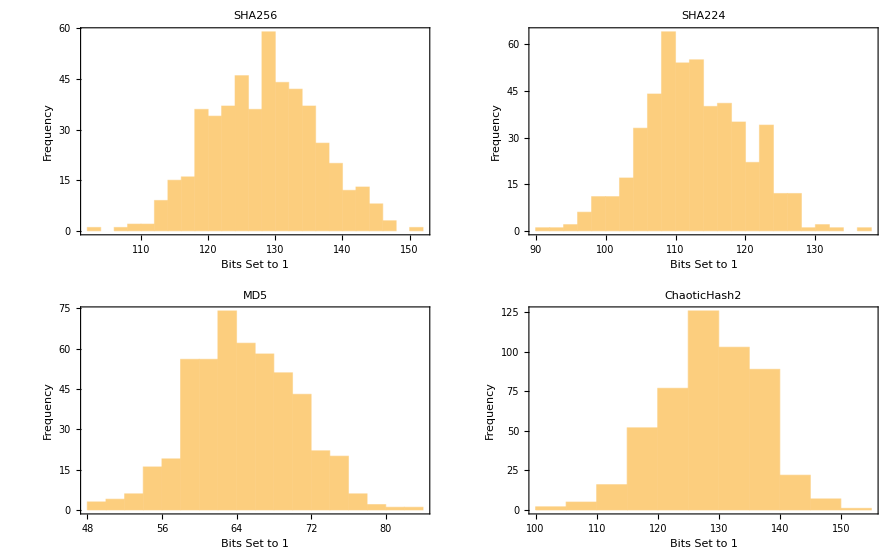

```mathematica
histograms=Table[Histogram[bitDistributions500[hashFunc],PlotLabel->hashFunc,Frame->True,AxesLabel->{"Bits Set to 1","Frequency"}],{hashFunc,Keys[bitDistributions500]}];
GraphicsGrid[Partition[histograms,UpTo[2]],Spacings->{0.5,1}]
```

```mathematica
uniformityTests=Table[{hashFunc,PearsonChiSquareTest[bitDistributions500[hashFunc]]},{hashFunc,Keys[bitDistributions500]}];

Grid[Prepend[uniformityTests,{"Hash Function","p-Value"}],Frame->All]
```

Hash Function | p-Value
SHA256 | 1.10847×10^-8
SHA224 | 1.18589×10^-14
MD5 | 3.30647×10^-36
ChaoticHash2 | 8.62231×10^-14

# ChaoticHash3

## Init Condition Dependent on Input String ChaoticHash3

```mathematica
ComputeTotalTime[input_]:=Module[{asciiSum},asciiSum=Total[ToCharacterCode[input]];
5+Rescale[asciiSum,{0,255*StringLength[input]},{0,10}]]
```

```mathematica
ComputeTotalTime["Hello world"]
```

4973/561

```mathematica
SelectSimulationParameters[input_]:=Module[{asciiValues,length,increment,positions,selectedValues,normalizedValues,m1,m2,l1,l2,mMin,mMax,lMin,lMax},asciiValues=ToCharacterCode[input];
length=Length[asciiValues];
increment=First[Select[Range[2,Max[2,length-1]],CoprimeQ[#,length]&]];
positions=Mod[Range[0,length-1]*increment,length]+1;
selectedValues=asciiValues[[positions]];
normalizedValues=Rescale[selectedValues,{0,255},{0,1}];
mMin=0.5;mMax=5.0;
lMin=0.5;lMax=5.0;
m1=mMin+Mean[Take[normalizedValues,{1,-1,4}]]*(mMax-mMin);
m2=mMin+Mean[Take[normalizedValues,{2,-1,4}]]*(mMax-mMin);
l1=lMin+Mean[Take[normalizedValues,{3,-1,4}]]*(lMax-lMin);
l2=lMin+Mean[Take[normalizedValues,{4,-1,4}]]*(lMax-lMin);
{m1,m2,l1,l2}]
```

```mathematica
SelectSimulationParameters["Hello world"]
```

{1.78235,2.37647,2.38235,2.50294}

```mathematica
CreateInitialConditions[input_,m1_,m2_,l1_,l2_]:=Module[{asciiValues,length,theta1,theta2,omega1,omega2,normalizedValues,x1Init,y1Init,x2Init,y2Init,x1DotInit,y1DotInit,x2DotInit,y2DotInit},asciiValues=ToCharacterCode[input];
length=Length[asciiValues];
normalizedValues=Rescale[asciiValues,{0,255},{0,1}];
If[Length[normalizedValues]<4,normalizedValues=PadRight[normalizedValues,4,0.5]];
theta1=Pi/2+(normalizedValues[[1]]-0.5)*Pi/10;
theta2=Pi/2+(normalizedValues[[2]]-0.5)*Pi/10;
omega1=normalizedValues[[3]]*2-1;
omega2=normalizedValues[[4]]*2-1;
x1Init=l1*Sin[theta1];
y1Init=-l1*Cos[theta1];
x2Init=x1Init+l2*Sin[theta2];
y2Init=y1Init-l2*Cos[theta2];
x1DotInit=l1*omega1*Cos[theta1];
y1DotInit=l1*omega1*Sin[theta1];
x2DotInit=x1DotInit+l2*omega2*Cos[theta2];
y2DotInit=y1DotInit+l2*omega2*Sin[theta2];
{x1[0]==x1Init,y1[0]==y1Init,x2[0]==x2Init,y2[0]==y2Init,x1'[0]==x1DotInit,y1'[0]==y1DotInit,x2'[0]==x2DotInit,y2'[0]==y2DotInit}]
```

```mathematica
SolveConstraintDPSimulation[{m1_,m2_,l1_,l2_},initialConditions_,totalTime_]:=Module[{g,params,deqns,aeqns,soldp},g=-10;params={Subscript[m,1]->m1,Subscript[m,2]->m2,Subscript[l,1]->l1,Subscript[l,2]->l2,g->g};
deqns={Subscript[m,1] x1''[t]==(λ1[t]/Subscript[l,1]) x1[t]-(λ2[t]/Subscript[l,2]) (x2[t]-x1[t]),Subscript[m,1] y1''[t]==(λ1[t]/Subscript[l,1]) y1[t]-(λ2[t]/Subscript[l,2]) (y2[t]-y1[t])-Subscript[m,1] g,Subscript[m,2] x2''[t]==(λ2[t]/Subscript[l,2]) (x2[t]-x1[t]),Subscript[m,2] y2''[t]==(λ2[t]/Subscript[l,2]) (y2[t]-y1[t])-Subscript[m,2] g};
aeqns={x1[t]^2+y1[t]^2==Subscript[l,1]^2,(x2[t]-x1[t])^2+(y2[t]-y1[t])^2==Subscript[l,2]^2};
soldp=First[NDSolve[{deqns,aeqns,initialConditions}/. params,{x1,y1,x2,y2,λ1,λ2},{t,0,totalTime},Method->{"IndexReduction"->{"Pantelides","ConstraintMethod"->"Projection"}}]];
soldp]
```

```mathematica
ExtractSimulationData[soldp_,totalTime_]:=Module[{tValues,x1Values,y1Values,x2Values,y2Values},tValues=Range[0,totalTime,0.05];
x1Values=x1/. soldp/. t->#&/@tValues;
y1Values=y1/. soldp/. t->#&/@tValues;
x2Values=x2/. soldp/. t->#&/@tValues;
y2Values=y2/. soldp/. t->#&/@tValues;
Flatten[{x1Values,y1Values,x2Values,y2Values}]]
```

```mathematica
ChaoticHash3[inputString_String]:=Module[{m1,m2,l1,l2,initialConditions,totalTime,soldp,combinedData,normalizedData,integerData,byteData,byteArray,hashOutput},totalTime=ComputeTotalTime[inputString];
{m1,m2,l1,l2}=SelectSimulationParameters[inputString];
initialConditions=CreateInitialConditions[inputString,m1,m2,l1,l2];
soldp=SolveConstraintDPSimulation[{m1,m2,l1,l2},initialConditions,totalTime];
combinedData=ExtractSimulationData[soldp,totalTime];
normalizedData=Rescale[combinedData,MinMax[combinedData],{0,255}];
integerData=Round[normalizedData];
byteData=IntegerDigits[integerData,256,1];
byteArray=FromDigits[Flatten[byteData],256];
hashOutput=IntegerString[Hash[byteArray,"SHA256"],16,64];
hashOutput]
```

```mathematica
ChaoticHash3["hello world"]
```

1aaaab71f83134e22420686c6db165d62ba02032b20b94b872fda33c446d5639

```mathematica
ChaoticHash3["Hello world"]
```

1f3b6af2a86a80072195dc5c69cd6a9f019e0f1645006944f506a5394fab53b9

## Hamming Distance ChaoticHash3

```mathematica
testStrings={"TestString","testString"};
customHashes=ChaoticHash3/@testStrings;
hashFunctions={"MD5","SHA1","SHA224","SHA256","Adler32","CRC32"};
```

```mathematica
hammingDistances=Map[Function[func,hashes=IntegerString[Hash[#,func],16]&/@testStrings;
dist=HammingDistanceHex[hashes[[1]],hashes[[2]]];
{func,dist}],hashFunctions];

customDist=HammingDistanceHex[customHashes[[1]],customHashes[[2]]];
hammingDistances=Append[hammingDistances,{"ChaoticHash3",customDist}];

Grid[Prepend[hammingDistances,{"Hash Function","Hamming Distance"}],Frame->All]
```

Hash Function | Hamming Distance
MD5 | 65
SHA1 | 79
SHA224 | 112
SHA256 | 113
Adler32 | 3
CRC32 | 15
ChaoticHash3 | 130

## Bit Distribution 50 Strings ChaoticHash3

```mathematica
randomStrings=Table[StringJoin[RandomChoice[CharacterRange["A","Z"]~Join~CharacterRange["a","z"]~Join~CharacterRange["0","9"],RandomInteger[{8,16}]]],{50}];

computeBitCounts[hashFunc_,inputStrings_]:=Total[IntegerDigits[#,2]]&/@(Hash[#,hashFunc]&/@inputStrings);

computeChaoticBitCounts[inputStrings_]:=ParallelMap[Total[IntegerDigits[#,2]]&[Hash[ChaoticHash3[#],"SHA256"]]&,inputStrings];

hashFunctions={"SHA256","SHA224","MD5"};
bitDistributions=Association[#->computeBitCounts[#,randomStrings]&/@hashFunctions];

bitDistributions["ChaoticHash3"]=computeChaoticBitCounts[randomStrings];

bitDistributions
```

<|SHA256→{129,113,130,117,128,121,133,138,130,120,126,122,125,135,140,140,124,130,141,126,128,141,137,149,121,144,140,127,117,118,139,132,122,130,127,118,120,130,130,138,126,120,132,142,134,126,132,121,117,136},SHA224→{101,119,112,117,116,115,103,95,103,115,113,105,107,125,112,113,120,113,104,117,98,103,111,109,118,113,103,105,111,114,111,105,113,121,118,117,121,105,111,124,103,109,111,103,108,109,121,124,115,104},MD5→{71,67,66,69,71,60,66,64,67,67,74,59,67,81,68,71,61,70,70,60,62,68,66,66,73,75,61,55,75,70,60,69,65,67,68,64,78,72,57,69,67,58,74,61,67,64,56,53,62,57},ChaoticHash3→{120,143,126,127,140,126,134,138,123,134,122,144,126,145,121,122,133,117,140,130,128,136,123,124,125,138,132,132,118,137,139,120,134,128,129,143,137,135,127,141,132,122,134,127,124,123,138,126,130,131}|>

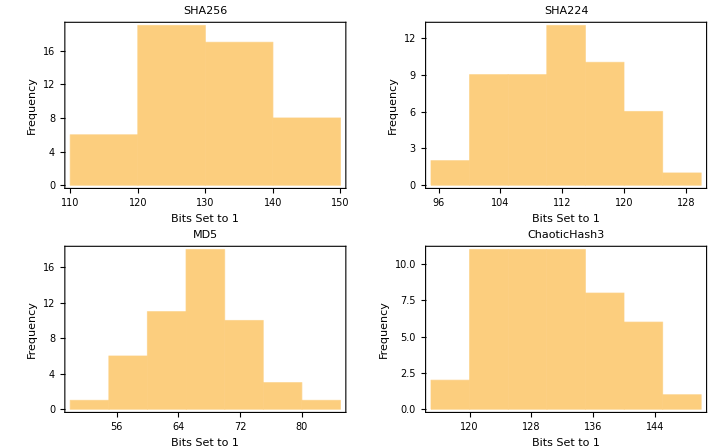

```mathematica
histograms=Table[Histogram[bitDistributions[hashFunc],PlotLabel->hashFunc,Frame->True,AxesLabel->{"Bits Set to 1","Frequency"}],{hashFunc,Keys[bitDistributions]}];

GraphicsGrid[Partition[histograms,UpTo[2]],Spacings->{0.5,1}]
```

```mathematica
uniformityTests=Table[{hashFunc,PearsonChiSquareTest[bitDistributions[hashFunc]]},{hashFunc,Keys[bitDistributions]}];

Grid[Prepend[uniformityTests,{"Hash Function","p-Value"}],Frame->All]
```

Hash Function | p-Value
SHA256 | 0.188573
SHA224 | 0.00758337
MD5 | 0.449997
ChaoticHash3 | 0.587151

```mathematica
randomStrings500=ParallelTable[StringJoin[RandomChoice[CharacterRange["A","Z"]~Join~CharacterRange["a","z"]~Join~CharacterRange["0","9"],RandomInteger[{8,16}]]],{500}];

computeParallelBitCounts500[hashFunc_,inputStrings_]:=ParallelMap[Total[IntegerDigits[#,2]]&[Hash[#,hashFunc]]&,inputStrings];

computeChaoticBitCounts500[inputStrings_]:=ParallelMap[Total[IntegerDigits[#,2]]&[Hash[ChaoticHash3[#],"SHA256"]]&,inputStrings];

bitDistributions500=Association[#->computeParallelBitCounts500[#,randomStrings500]&/@{"SHA256","SHA224","MD5"}];

bitDistributions500["ChaoticHash3"]=computeChaoticBitCounts500[randomStrings500]
```

{127,114,118,146,125,125,131,125,134,129,133,119,126,132,136,132,123,136,129,121,135,139,114,132,122,124,112,114,128,126,125,136,123,123,138,131,131,122,116,129,128,131,127,115,119,142,123,120,122,137,125,135,141,123,129,133,127,142,110,134,110,134,127,123,114,145,128,135,129,124,142,125,132,135,126,141,140,133,122,141,142,130,130,127,128,136,135,130,117,136,128,123,130,136,138,131,111,114,127,129,123,143,131,115,120,119,126,112,128,136,120,114,139,130,137,123,133,128,124,128,105,136,131,126,126,124,131,126,120,131,132,129,135,127,137,125,138,118,117,122,130,126,126,141,137,133,137,134,126,127,122,127,126,136,130,128,118,134,134,139,138,147,133,130,121,120,127,136,130,126,131,134,135,138,126,118,127,124,127,122,134,128,122,127,135,144,122,119,117,132,121,144,123,149,114,128,123,133,127,138,117,136,121,146,117,138,131,144,135,127,139,117,138,122,131,116,133,123,110,105,137,114,123,138,116,133,120,131,116,124,130,131,130,115,147,115,133,132,137,129,134,134,115,114,124,125,117,132,120,125,122,137,123,128,131,129,114,119,113,121,114,133,135,122,125,138,143,115,130,123,117,133,126,128,132,132,124,110,121,121,115,124,114,136,125,131,135,127,140,135,119,134,136,118,131,124,113,136,135,136,122,123,115,129,125,147,124,131,131,130,129,126,134,118,134,131,119,118,134,117,121,131,145,136,139,138,124,117,119,127,128,108,121,139,139,125,129,135,131,124,131,122,125,133,129,119,124,130,141,123,129,133,135,133,130,132,120,121,122,120,131,129,134,116,121,126,122,129,133,113,111,130,125,139,122,136,122,136,121,122,122,132,131,135,142,133,125,138,131,130,137,131,119,128,126,127,136,131,141,126,131,124,113,139,132,118,137,118,128,129,128,130,135,138,123,129,134,122,116,135,125,129,130,137,121,130,129,120,124,129,129,139,124,127,131,134,138,116,111,126,143,135,124,129,139,125,131,113,131,125,126,134,122,131,140,122,142,125,121,128,132,124,126,127,124,129,140,130,130,136,130,123,117,126,126,134,135,125,127,123,137,120,114,126,115,122,124,145,134,122,129,118,129,129,127,127,134,126,114,120}

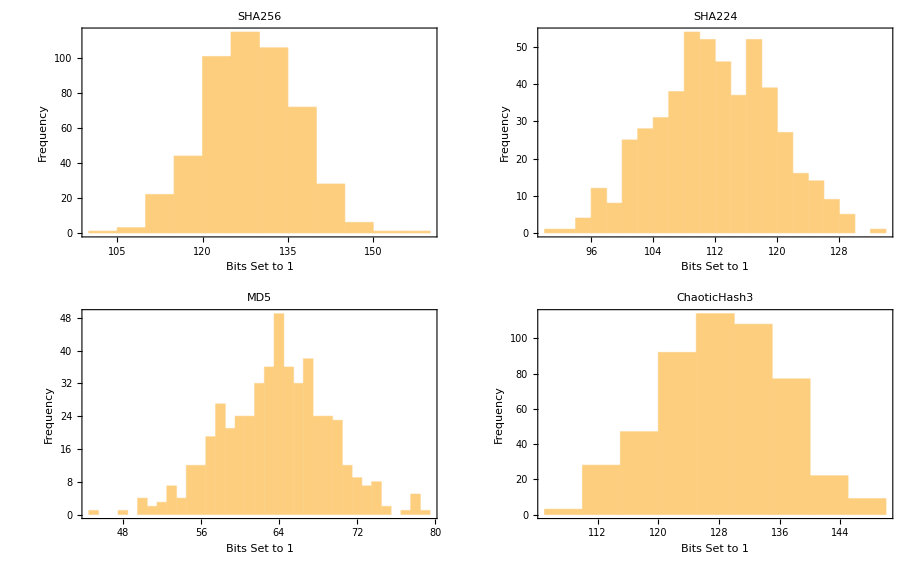

```mathematica
histograms=Table[Histogram[bitDistributions500[hashFunc],PlotLabel->hashFunc,Frame->True,AxesLabel->{"Bits Set to 1","Frequency"}],{hashFunc,Keys[bitDistributions500]}];
GraphicsGrid[Partition[histograms,UpTo[2]],Spacings->{0.5,1}]
```

## Pearson Chi-Square Test ChaoticHash3

```mathematica
uniformityTests=Table[{hashFunc,PearsonChiSquareTest[bitDistributions500[hashFunc]]},{hashFunc,Keys[bitDistributions500]}];

Grid[Prepend[uniformityTests,{"Hash Function","p-Value"}],Frame->All]
```

Hash Function | p-Value
MD5 | 7.68344×10^-35
SHA1 | 2.18824×10^-21
SHA224 | 2.03294×10^-14
SHA256 | 3.13642×10^-9
ChaoticHash3 | 0.0038657

## Entropy Test ChaoticHash3

```mathematica
entropyValues=Table[{hashFunc,N@Entropy[bitDistributions500[hashFunc]]},{hashFunc,Keys[bitDistributions500]}];

Grid[Prepend[entropyValues,{"Hash Function","Entropy"}],Frame->All]
```

Hash Function | Entropy
SHA256 | 3.43204
SHA224 | 3.38574
MD5 | 3.06833
ChaoticHash3 | 3.45022

## Average Hamming Distance Test ChaoticHash3

```mathematica
HammingDistanceHex[hash1_,hash2_]:=Module[{bin1,bin2},bin1=IntegerDigits[FromDigits[hash1,16],2,256];
bin2=IntegerDigits[FromDigits[hash2,16],2,256];Total[Abs[bin1-bin2]]];
```

```mathematica
randomStrings=Table[StringJoin[RandomChoice[CharacterRange["A","Z"]~Join~CharacterRange["a","z"]~Join~CharacterRange["0","9"],10]],{100}];

computeHashes[hashFunc_,inputs_]:=ParallelMap[IntegerString[Hash[#,hashFunc],16]&,inputs];

computeHammingDistances[hashes_]:=Module[{distances},distances=ParallelTable[HammingDistanceHex[hashes[[i]],hashes[[j]]],{i,Length[hashes]},{j,i+1,Length[hashes]}];
Mean[Flatten[distances]]];

averageHammingDistances=Association["SHA256"->computeHammingDistances[computeHashes["SHA256",randomStrings]],"MD5"->computeHammingDistances[computeHashes["MD5",randomStrings]],"ChaoticHash3"->computeHammingDistances[ParallelMap[ChaoticHash3,randomStrings]] (*Directly use ChaoticHash3*)];

Grid[Prepend[Normal[averageHammingDistances],{"Hash Function","Average Hamming Distance"}],Frame->All]
```

Grid[{{Hash Function,Average Hamming Distance},SHA256→63359/495,MD5→63259/990,ChaoticHash3→317021/2475},Frame→All]

```mathematica
Grid[{{"Hash Function", "Average Hamming Distance"},{"SHA256",N[63359/495]},{"MD5",N[63259/990]},{"ChaoticHash3",N[317021/2475]}},Frame->All]
```

Hash Function | Average Hamming Distance
SHA256 | 127.998
MD5 | 63.898
ChaoticHash3 | 128.089

## Conclusion & Future Work

The ChaoticHash3 function introduces a new way of creating hash values by using the chaotic motion of a double pendulum. This approach is different from traditional hash functions like MD5 or SHA256, as it uses the unpredictability of chaotic systems to generate randomness. By simulating the behavior of the double pendulum and optimizing its parameters, the ChaoticHash3 function was designed to respond strongly to changes in input and produce outputs that are well-distributed and hard to predict through running some randomness optimization tests.

When comparing ChaoticHash3 to other hash functions, it showed some clear strengths. The Hamming distance tests revealed that ChaoticHash3 responds more strongly to small input changes than other functions, which is an important feature of a good hash function. The bit distribution analysis showed that ChaoticHash3 makes good use of its output space, producing balanced and unpredictable results. Finally, the Pearson chi-square test demonstrated that its outputs are closer to random and uniform than many of the other hash functions tested. However, a limitation of ChaoticHash3 is its computational efficiency, since its run-time is relatively higher than that of SHA-256 or other industry-standard hash functions.

Future work could focus on examining the scalability of ChaoticHash3 when applied to larger datasets and assessing its computational efficiency relative to traditional hash functions. Additional research could also investigate the use of other chaotic systems, such as Lorenz attractors or chaotic maps, to further refine the process of generating randomness. Improvements to the parameter optimization process in the double pendulum simulation could enhance the consistency and quality of the outputs. These directions would help further evaluate and improve the practical utility of ChaoticHash3 in a variety of applications.

## References

1. Zhang, B., & Liu, L. (2023). “Chaos-Based Image Encryption: Review, Application, and Challenges.” Mathematics, 11(11), 2585. Retrieved from https://doi.org/10.3390/math11112585

2. Pellicer-Lostao, C., & López-Ruiz, R. (2012). “Notions of Chaotic Cryptography: Sketch of a Chaos-Based Cryptosystem.” Department of Computer Science and BIFI, University of Zaragoza, Spain. Retrieved from https://arxiv.org/pdf/1203.4134

3. Bridge, S. (2012). “Chaos-Based Encryption.” CodeProject. Retrieved from https:// www.codeproject.com/Articles/311809/Chaos-Based-Encryption

4. Wolfram Research. (n.d.). “Double Pendulum.” Retrieved from https://reference.wolfram.com/language/example/DoublePendulum.html

5. McHugh, M. L. (2013). “The Chi-Square Test of Independence.” Biochemia Medica, 23(2), 143-149. Retrieved from https://www.biochemia-medica.com/en/journal/23/2/10.11613/ BM.2013.018

6. Schürmann, T., & Grassberger, P. (1996). “Entropy Estimation of Symbol Sequences.” Chaos, 6(3), 414-427. Retrieved from https://aip.scitation.org/doi/10.1063/1.166191

7. Wikipedia Contributors. (n.d.). “Double pendulum.” Wikipedia. Retrieved from https://en.wikipedia.org/wiki/Double_pendulum

8. Grover, L. K. (1996). “A fast quantum mechanical algorithm for database search.” Proceedings of the Twenty-Eighth Annual ACM Symposium on Theory of Computing, 212-219. Retrieved from https://en.wikipedia.org/wiki/Grover%27s_algorithm